```mathematica
p[t_]=20*(t^(-1/2))*Exp[-(10-3*t)^2/(0.5*t)]
```

(20 ⅇ^(-(2. (10-3 t)^2)/t))/(√t)

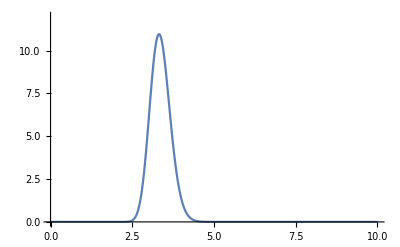

```mathematica
Plot[p[t],{t,-1,10},PlotRange -> {0,12}]
```

```mathematica
dpdt[t_]=D[p[t],t]
```

-(10 ⅇ^(-(2. (10-3 t)^2)/t))/t^(3/2)+(20 ⅇ^(-(2. (10-3 t)^2)/t) ((2. (10-3 t)^2)/t^2+(12. (10-3 t))/t))/(√t)

```mathematica
(*PART B*)
```

```mathematica
d2pdt2[s_]=D[dpdt[s],s];
tn[s_]=s-dpdt[s] / d2pdt2[s];
NestList[tn,3.33,10]
```

{3.33,3.31941,3.31947,3.31947,3.31947,3.31947,3.31947,3.31947,3.31947,3.31947,3.31947}

```mathematica
(*PART C*)
```

```mathematica
p[1]
p[3.195]
p[100]
```

5.49757×10^-42

10.0455

6.57221003812×10^-731

```mathematica
(*PART D*)
```

```mathematica
g[t_] = p[t]-1;
dgdt[t_]=D[g[t],t];
tn2[s_]=s-g[s] / dpdt[s];
NestList[tn2,3,10]
NestList[tn2,4,10]
```

{3,2.79502,2.73309,2.71991,2.71932,2.71932,2.71932,2.71932,2.71932,2.71932,2.71932}

{4,4.04642,4.05222,4.0523,4.0523,4.0523,4.0523,4.0523,4.0523,4.0523,4.0523}

```mathematica
(*Check answers*)
p[2.719321]
p[4.052300]
```

0.999991

1.